0.

0.367879

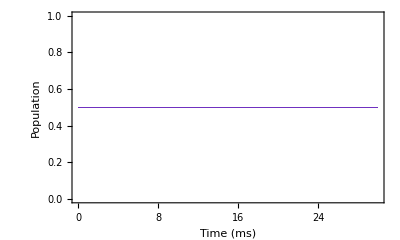

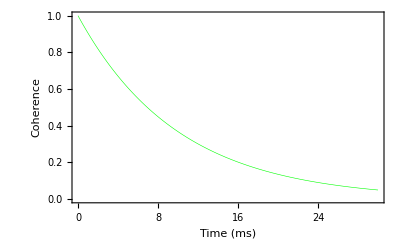

```mathematica
(*Two-level system*)
Remove["`*"];
fontsize1=18;fontsize2=18;axesize=15;thickness=0.001;thickness1=0.004;

(*Parameters and equations*)
γ=0.1;σp={{0,1},{0,0}};σn={{0,0},{1,0}};
inis=IdentityMatrix[2]/2+PauliMatrix[1]/2;
tran=3/γ;tstep=tran/1000;
sol=NDSolve[{ρ'[t]==-γ*(ρ[t]-σp.ρ[t].σn-σn.ρ[t].σp),ρ[0]==inis},ρ,{t,0,tran}];
ρ[t_]=sol[[1,1,2]][t];
tap0=Table[{t,ρ[t][[1,1]]},{t,0,tran,tstep}];
tap1=Table[{t,ρ[t][[2,2]]},{t,0,tran,tstep}];
tac=Table[{t,2*Abs[ρ[t][[1,2]]]},{t,0,tran,tstep}];

(*Plot*)
2*ρ[1/(2γ)][[1,1]]-1
2*Abs[ρ[1/(γ)][[1,2]]]
ListPlot[{tap0,tap1},Joined->True,PlotRange->All,AspectRatio->0.6,Frame->True,Axes->False,PlotStyle->{Directive[Red,Thickness[thickness]],Directive[Blue,Thickness[thickness]]},FrameLabel->{Text[Style["Time (ms)",Bold,Black,fontsize1]],Text[Style["Population",Bold,fontsize2]]}, FrameStyle->Directive[Arrowheads[0.05],Thickness[thickness],Black,axesize]]
ListPlot[tac,Joined->True,PlotRange->All,AspectRatio->0.6,Frame->True,Axes->False,PlotStyle->{Directive[Green,Thickness[thickness]]},FrameLabel->{Text[Style["Time (ms)",Bold,Black,fontsize1]],Text[Style["Coherence",Bold,fontsize2]]}, FrameStyle->Directive[Arrowheads[0.05],Thickness[thickness],Black,axesize]]
```

5.58659

{{5.58659,1.06595×10^-7}}

0.367879

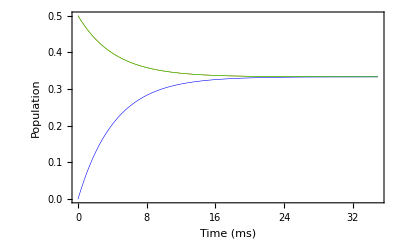

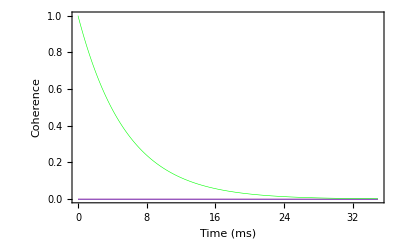

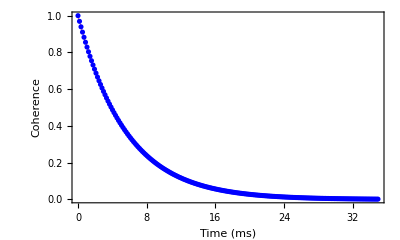

```mathematica
(*Three-level system: population and coherence*)
Remove["`*"];
fontsize1=18;fontsize2=18;axesize=15;thickness=0.001;thickness1=0.004;

(*Parameters and equations*)
γ01=0.0788;0.1;γ0n1=0.0788;0.1;γ1n1=0.1002;0.13;num=3;
σp1n1=σn1n1=σp0n1=σn0n1=σp01=σn01=ConstantArray[0,{3,3}];
pro01=pro0n1=pro1n1=IdentityMatrix[3];
σp01[[1,2]]=1;σn01[[2,1]]=1;σp0n1[[2,3]]=1;
σn0n1[[3,2]]=1;σp1n1[[1,3]]=1;σn1n1[[3,1]]=1;
pro01[[3,3]]=0;pro0n1[[1,1]]=0;pro1n1[[2,2]]=0;
tains={{{1,1,0},{1,1,0},{0,0,0}}/2,{{0,0,0},{0,1,1},{0,1,1}}/2,{{1,0,1},{0,0,0},{1,0,1}}/2};
inis=tains[[num]];tran=3/Mean[{γ01,γ0n1,γ1n1}];tstep=tran/200;
sol=NDSolve[{ρ'[t]==-γ01*((pro01.ρ[t]+ρ[t].pro01)/2-σp01.ρ[t].σn01-σn01.ρ[t].σp01)-γ0n1*((pro0n1.ρ[t]+ρ[t].pro0n1)/2-σp0n1.ρ[t].σn0n1-σn0n1.ρ[t].σp0n1)-γ1n1*((pro1n1.ρ[t]+ρ[t].pro1n1)/2-σp1n1.ρ[t].σn1n1-σn1n1.ρ[t].σp1n1),ρ[0]==inis},ρ,{t,0,tran}];
ρ[t_]=sol[[1,1,2]][t];
tap1=Table[{t,ρ[t][[1,1]]},{t,0,tran,tstep}];tap0=Table[{t,ρ[t][[2,2]]},{t,0,tran,tstep}];tapn1=Table[{t,ρ[t][[3,3]]},{t,0,tran,tstep}];
tac01=Table[{t,2*Abs[ρ[t][[1,2]]]},{t,0,tran,tstep}];
tac0n1=Table[{t,2*Abs[ρ[t][[2,3]]]},{t,0,tran,tstep}];
tac1n1=Table[{t,2*Abs[ρ[t][[1,3]]]},{t,0,tran,tstep}];
tac={tac01,tac0n1,tac1n1};

(*Fitting*)
tat10={1/(γ01+γ0n1/2+γ1n1/2),1/(γ01/2+γ0n1+γ1n1/2),1/(γ01/2+γ0n1/2+γ1n1)};
t10=tat10[[num]]
f[t_]=Exp[-t/t1];
nfcre=NonlinearModelFit[tac[[num]],f[t],{{t1,t10}},t];
noval=nfcre["ParameterConfidenceIntervals",ConfidenceLevel->0.683];
p=1-nfcre["EstimatedVariance",ConfidenceLevel->.683];
fitpa=Table[{(noval[[i,1]]+noval[[i,2]])/2,Abs[noval[[i,1]]-noval[[i,2]]]/2},{i,1,Length[noval]}]
{t1}=Transpose[fitpa][[1]];

(*Plot*)
2*Abs[ρ[t10][[num,Mod[num+1,3,1]]]]
ListPlot[{tap1,tap0,tapn1},Joined->True,PlotRange->All,AspectRatio->0.6,Frame->True,Axes->False,PlotStyle->{Directive[Red,Thickness[thickness]],Directive[Blue,Thickness[thickness]],Directive[Green,Thickness[thickness]]},FrameLabel->{Text[Style["Time (ms)",Bold,Black,fontsize1]],Text[Style["Population",Bold,fontsize2]]}, FrameStyle->Directive[Arrowheads[0.05],Thickness[thickness],Black,axesize]]
ListPlot[{tac01,tac0n1,tac1n1},Joined->True,PlotRange->All,AspectRatio->0.6,Frame->True,Axes->False,PlotStyle->{Directive[Red,Thickness[thickness]],Directive[Blue,Thickness[thickness]],Directive[Green,Thickness[thickness]]},FrameLabel->{Text[Style["Time (ms)",Bold,Black,fontsize1]],Text[Style["Coherence",Bold,fontsize2]]}, FrameStyle->Directive[Arrowheads[0.05],Thickness[thickness],Black,axesize]]
p=Plot[f[t],{t,0,tran},PlotRange->All,AspectRatio->0.6,Frame->True,Axes->False,PlotStyle->{Directive[Red,Thickness[thickness]]},FrameLabel->{Text[Style["Time (ms)",Bold,Black,fontsize1]],Text[Style["Coherence",Bold,fontsize2]]}, FrameStyle->Directive[Arrowheads[0.05],Thickness[thickness],Black,axesize]];
lp=ListPlot[tac[[num]],PlotRange->All,AspectRatio->0.6,Frame->True,Axes->False,PlotStyle->{Directive[Blue,Thickness[thickness]]},FrameLabel->{Text[Style["Time (ms)",Bold,Black,fontsize1]],Text[Style["Coherence",Bold,fontsize2]]}, FrameStyle->Directive[Arrowheads[0.05],Thickness[thickness],Black,axesize]];
Show[p,lp]
```

0.36788

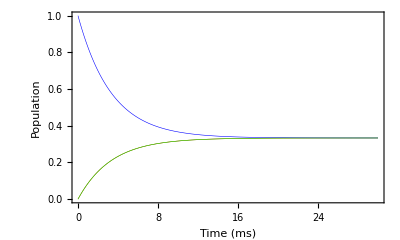

```mathematica
(*Three-level system: population*)
Remove["`*"];
fontsize1=18;fontsize2=18;axesize=15;thickness=0.001;thickness1=0.004;

(*Parameters and equations*)
γ01=0.1;γ0n1=0.1;γ1n1=0.15;
σp1n1=σn1n1=σp0n1=σn0n1=σp01=σn01=ConstantArray[0,{3,3}];
pro01=pro0n1=pro1n1=IdentityMatrix[3];
σp01[[1,2]]=1;σn01[[2,1]]=1;σp0n1[[2,3]]=1;
σn0n1[[3,2]]=1;σp1n1[[1,3]]=1;σn1n1[[3,1]]=1;
pro01[[3,3]]=0;pro0n1[[1,1]]=0;pro1n1[[2,2]]=0;
inis={{0,0,0},{0,1,0},{0,0,0}};{{0,0,0},{0,0,0},{0,0,1}};
tran=3/Min[γ01,γ0n1,γ1n1];tstep=tran/1000;
sol=NDSolve[{ρ'[t]==-γ01*((pro01.ρ[t]+ρ[t].pro01)/2-σp01.ρ[t].σn01-σn01.ρ[t].σp01)-γ0n1*((pro0n1.ρ[t]+ρ[t].pro0n1)/2-σp0n1.ρ[t].σn0n1-σn0n1.ρ[t].σp0n1)-γ1n1*((pro1n1.ρ[t]+ρ[t].pro1n1)/2-σp1n1.ρ[t].σn1n1-σn1n1.ρ[t].σp1n1),ρ[0]==inis},ρ,{t,0,tran}];
ρ[t_]=sol[[1,1,2]][t];
tap1=Table[{t,ρ[t][[1,1]]},{t,0,tran,tstep}];tap0=Table[{t,ρ[t][[2,2]]},{t,0,tran,tstep}];tapn1=Table[{t,ρ[t][[3,3]]},{t,0,tran,tstep}];

(*Plot*)
(3*ρ[1/(3γ01)][[2,2]]-1)/2
ListPlot[{tap1,tap0,tapn1},Joined->True,PlotRange->All,AspectRatio->0.6,Frame->True,Axes->False,PlotStyle->{Directive[Red,Thickness[thickness]],Directive[Blue,Thickness[thickness]],Directive[Green,Thickness[thickness]]},FrameLabel->{Text[Style["Time (ms)",Bold,Black,fontsize1]],Text[Style["Population",Bold,fontsize2]]}, FrameStyle->Directive[Arrowheads[0.05],Thickness[thickness],Black,axesize]]
```